# Initialization tool for root shoot model

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*in this version the rates are per capita*)
S=2;R=1;
β=.2;
λ=100;
F[x_,y_]:=Min[x,y];
(*growth rate of root and shoot*)
jRG=F[ρC S/R,1];
jSG=F[1,ρN/β R/S];
(*N and C shared (unbuffered)*)
jN=1-jRG;
jC=1-jSG;
vρN=λ (jN-ρN);
vρC=λ (jC-ρC);
vars={ρN,ρC};
(*find equilibria*)
TableForm[eqs=Quiet@NSolve[{vρN==0,vρC==0},vars]]
```

ρN→0. | ρC→1.
ρN→0.25 | ρC→0.375
ρN→1. | ρC→0

```mathematica
JacobianMatrix[f_,x_]:=Outer[D,f,x];
```

```mathematica
eq=eqs[[2]];
```

```mathematica
eigensystem=Eigensystem[JacobianMatrix[{vρN,vρC},vars]/.eq];
Grid[Table[{"eigenvalue :",eigensystem[[1,i]],"eigenvector :",MatrixForm[eigensystem[[2,i]]]},{i,Length@eigensystem[[1]]}]]
```

eigenvalue : | -323.607 | eigenvector : | (0.666667
0.745356)
eigenvalue : | 123.607 | eigenvector : | (0.666667
-0.745356)

```mathematica
eigenvec=Re@eigensystem[[2,Ordering[eigensystem[[1]],1][[1]]]]
```

{0.666667,0.745356}

```mathematica
vectorplotlegend=Style[Grid[{{Graphics[{AbsolutePointSize[10],Red,Point[{0,0}]},ImageSize->{12,12}],"Equilibrium"},{Plot[.5,{x,0,1},PlotStyle->{{AbsoluteThickness[3.5],Black}},Axes->None,ImageSize->{20,20}],"Separatrix"}},Alignment->{{Center,Left}}],16,FontFamily->"Times"];
```

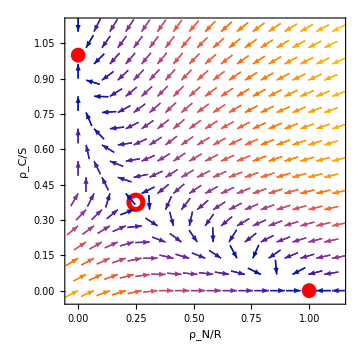

```mathematica
tminsep=-10;tmaxsep=0;ϵ=-.0001;
dosol[ϵ_]:=NDSolve[#[[1]]==(#[[2]]/.((#->#[t])&/@vars))&/@{
ρN'[t]==vρN,
ρC'[t]==vρC,
ρN[0]==(ρN/.eq)+ϵ eigenvec[[1]],
ρC[0]==(ρC/.eq)+ϵ eigenvec[[2]]
},
vars,
{t,tminsep,tmaxsep}][[1]];
sol1=dosol[ϵ];
sol2=dosol[-ϵ];

(Export["root-shoot-fast-dynamics-plane.pdf",#];#)&@Show[{
VectorPlot[{vρN/R, vρC/S}, {ρN,0,1.1},{ρC,0,1.1},VectorPoints->17,FrameLabel->{"ρ_N/R","ρ_C/S"},Epilog->Join[{PointSize[.04],Red},Table[Piecewise[{{{Thickness[.01],Circle[#,Scaled@.025]}&, i==2}, {Disk[#,Scaled@.026]&, True}}]@vars/.eqs[[i]],{i,Length@eqs}]],ImageSize->Medium(*,PlotLegends->Automatic*),VectorMarkers->Placed["Arrow","End"](*,VectorColorFunction->None,VectorStyle->Blue*)],
ParametricPlot[{{ρN[t],ρC[t]}/.sol1,{ρN[t],ρC[t]}/.sol2},{t,tminsep,tmaxsep},PlotStyle->{{Thickness[.015],Black}}]
},LabelStyle->16]
```